```mathematica
makeSystem[A_, a_List,γ_List, ϵ_List]:=Module[{n=Length[A], varsV,varsw, lhsV, rhsV, lhsw, rhsw}, (*n here is the total number of heart cells*)
varsV=Table[Subscript[V, i][t],{i,1,n}];
varsw=Table[Subscript[w, i][t],{i,1,n}];
lhsV=D[varsV,t];
rhsV=Table[varsV[[i]](varsV[[i]]-a[[i]])(1-varsV[[i]])-varsw[[i]],{i,1,n}];
rhsV+=(A-DiagonalMatrix[Total/@A]).varsV;
lhsw=D[varsw,t];
rhsw=Table[varsV[[i]]-γ[[i]]varsw[[i]],{i,1,n}];

Join[Thread[lhsV==ϵ^-1 rhsV],Thread[lhsw==rhsw]]
]
makeSphereConnectionMatrix[n_,α_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i+j n;
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j];
kSouth=getIndex[i, Mod[j+1,n]];
kNorth=getIndex[i, Mod[j+n-1,n]];
kEast=getIndex[Mod[i+1,n],j];
kWest=getIndex[Mod[i+n-1,n], j];
A[[k+1,kSouth+1]]=α;
A[[k+1,kNorth+1]]=α;
A[[k+1,kEast+1]]=α;
A[[k+1,kWest+1]]=α
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

make2DConnectionMatrix[n_,αNW_, αSE_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i+j n;
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j];

kSouth=getIndex[i, Mod[j+1,n]];
kNorth=getIndex[i, Mod[j+n-1,n]];
kEast=getIndex[Mod[i+1,n],j];
kWest=getIndex[Mod[i+n-1,n], j];
If [i==n-j, ,
];
If[(k+1)<=n*(n-1),A[[k+1,kSouth+1]]=αSE];
If[(k+1)>n,A[[k+1,kNorth+1]]=αNW];
If[Mod[(k+1),n]!=0,A[[k+1,kEast+1]]=αSE];
If[Mod[(k+1), n]!=1,A[[k+1,kWest+1]]=αNW]
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

dataMatrix[τ_,n_]:=Table[Subscript[V, j+(i-1) n][t],{i,1,n},{j,1,n}]/.solution/.t->τ
```

```mathematica
n=6; (*size of the spatial grid*)
cMatrix = makeSphereConnectionMatrix[n, 1/50];
MatrixForm[cMatrix];
aList = Table[0.01, Length@cMatrix];
γList = Table[0.5, Length@cMatrix];
ϵ=0.008;
ϵList = Table[ϵ, Length@cMatrix];
ODEsys = makeSystem[cMatrix, aList, γList, ϵList];

(*Apply periodic stimuli to the 1st cell*)
duration=0.1;  strength=0.05; frequency=0.5;
stimuliTrain[t_, A_,duty_, freq_]:=A*UnitBox[Mod[t*freq,1.]/(2. duty)];
S=stimuliTrain[t-(duration+1/2), strength, duration, frequency];
s=1; (*index of cell stimulated*)
ODEsys[[s, 2]]+= S*ϵ^-1;

(*Solve system*)
tmin=0;
tmax=10;
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];
```

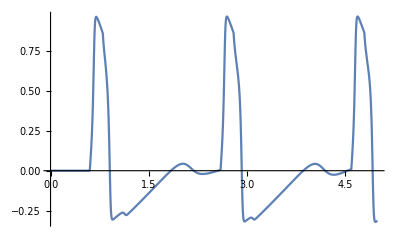

```mathematica
Plot[Subscript[V, 1][t]/.solution,{t,0,5},PlotRange->All]
```

```mathematica
figTable = Table[MatrixPlot[dataMatrix[t,n],ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False],{t,tmin,tmax,0.05}];
```

```mathematica
ListAnimate[figTable, ImageSize->Full]
```